```mathematica
(*this is the mathematica notebook i used to quickly generate many of the graphs seen in my slides, without all the Export[] statements used to save the figures to disk. the only notable thing is that examples 2 and 5 are random, so that running them again will generate a different result*)
```

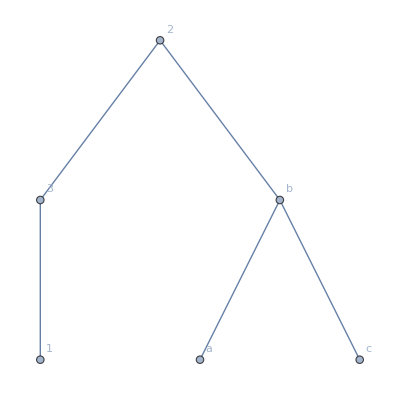

```mathematica
v={1, 2, 3, 4,5,6};
e={{1,3},{4,6},{5,6},{6,2},{2,3}};
example1=Graph[v,e,VertexLabels->{1->"1",2->"2",3->"3",4->"a",6->"b",5->"c"}]
```

```mathematica
randmat=RandomReal[1,{6,6}];
randmat=Round[randmat]
example2=AdjacencyGraph[randmat]
```

{{0,1,0,0,0,0},{0,0,0,1,0,0},{1,0,0,1,1,1},{0,1,0,1,1,1},{0,1,0,0,0,1},{1,0,0,0,0,0}}

-Graphics-

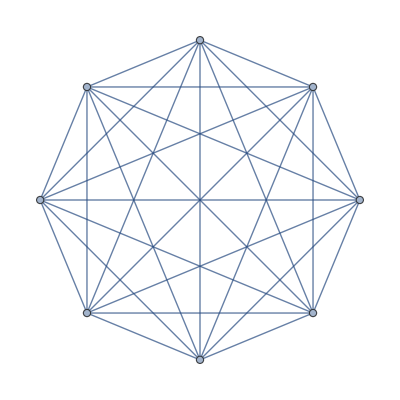

```mathematica
example3=CompleteGraph[8]
```

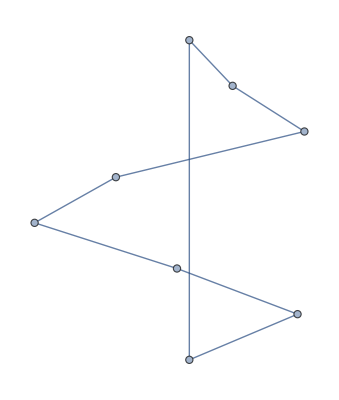

```mathematica
example4=CycleGraph[8,GraphLayout->"SpiralEmbedding"]
```

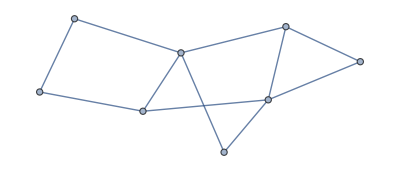

{1<->4,2<->8,3<->7,5<->6}

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
example5=RandomGraph[{8,11}]
FindIndependentEdgeSet[example5]
```

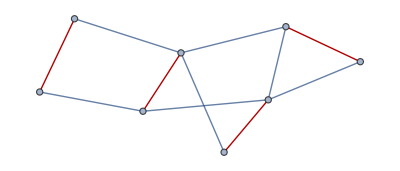

```mathematica
example5soln=HighlightGraph[example5,{1<->4,2<->8,3<->7,5<->6}]
```

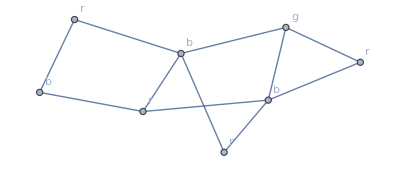

```mathematica
example6=AdjacencyGraph[{{0,0,0,1,1,0,1,0},{0,0,0,0,1,0,0,1},{0,0,0,1,0,0,1,0},{1,0,1,0,0,1,0,1},{1,1,0,0,0,1,0,1},{0,0,0,1,1,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,1,1,0,0,0}},VertexLabels->{1->"r",2->"r",3->"r",4->"b",5->"b",6->"r",7->"b",8->"g"}]
```

```mathematica
EdgeList[example6]
```

{1<->4,1<->5,1<->7,2<->5,2<->8,3<->4,3<->7,4<->6,4<->8,5<->6,5<->8}

```mathematica
BipartiteGraphQ[example6]
```

False